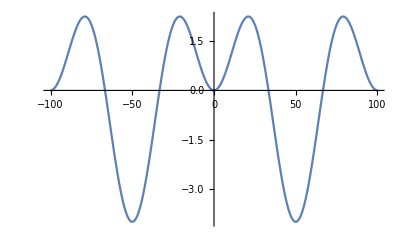

```mathematica
ψ[x_]:=2*Exp[2*Pi*I*x/100]-2*Exp[-2*Pi*I*x/50]
f0=ListLinePlot[Table[{y,(Re[N[ψ[y]]]+0*Im[N[ψ[y]]])},{y,-100,100}]];
f1=ListLinePlot[Table[{z,(Re[N[ψ[z]]]+0*Im[N[ψ[z]]])^2},{z,-100,100}]];
Show[f0]
```

```mathematica
ψ2[x_]:=Exp[(-x^2 + I*x*70*Pi)/1200]
f10=ListLinePlot[Table[{y,(Re[N[ψ2[y]]]+0*Im[N[ψ2[y]]])},{y,-100,100}],PlotStyle->Thickness[0.02],Axes->{False,True},TicksStyle->Large,PlotRange->{-1,1.2}];
f21=ListLinePlot[Table[{z,(Re[N[ψ2[z]]]+0*Im[N[ψ2[z]]])^2},{z,-10,10}]];
Show[f10]
```

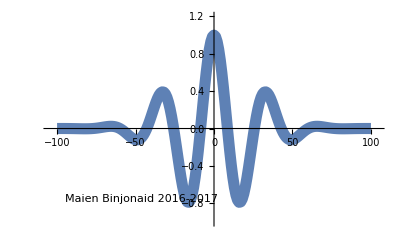

```mathematica
f3[x_]:=(2*Exp[2*Pi*I*x/100]-2*Exp[-2*Pi*I*x/50])*Exp[0.001]
ListLinePlot[Table[{y,(Re[N[f3[y]]]+0*Im[N[f3[y]]])},{y,-100,100}]]
```

-Graphics-